4 √2

3.77124

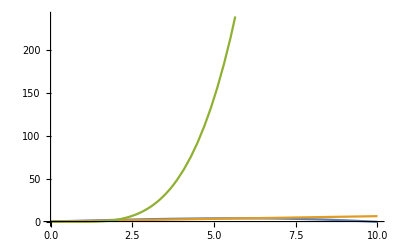

2.0174643744016221750953541497398127177859613360629×10^10

```mathematica
TransMatrixFlint[β_,ϵ_,f_,p_]:=Module[{points,g,mtx},points=Range[0,6,ϵ];
(*connect points up into a linear graph*)g=RelationGraph[Abs[#1-#2]==ϵ&,points,DirectedEdges->True];
(*set edge weights*)g=With[{el=EdgeList[g]},Graph[el,EdgeWeight->(#->p[#[[1]],#[[2]],β,ϵ,f]&/@el)]];
(*get the weight matrix*)mtx=WeightedAdjacencyMatrix[g];
(*need to make up the difference for cases when x==y if row is not normalized*)mtx+DiagonalMatrix[1-Total/@mtx]]

f[x_]:=-x^3*(1/2)^2/24+x
ccrit =2* Sqrt[8]
Ecrit = f[ccrit]//N

f1[x_]:=(Ecrit/6)*x
doublewell[x_]:=((1/2)*x^2-1)*(1/2)*x^2
Plot[{f[x],f1[x], doublewell[x]},{x,0,10}]



p[x_,y_,β_,ϵ_,f_]:=If[Abs[y-x]≠ϵ,0,Piecewise[{{1/3000,f[y]<f[x]},{1/3000 Exp[(f[x]-f[y])/β],f[y]>f[x]}},0]]

temperatures={25/100,30/100,35/100,40/100, 50/100,60/100};

(*use rationals here for best precision*)
trmtx=TransMatrixFlint[temperatures[[1]],1,f,p];

Total[trmtx];


trmtx1=TransMatrixFlint[temperatures[[2]],1,f,p];
(*MatrixPlot[trmtx]*)
(*use a high precision on trmtx*)
A=DiscreteMarkovProcess[1,SetPrecision[trmtx,80]];
A1=DiscreteMarkovProcess[1,SetPrecision[trmtx1,80]];

EscTime=FirstPassageTimeDistribution[A,7];
EscTime1=FirstPassageTimeDistribution[A1,7];

Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,SetPrecision[TransMatrixFlint[temperatures[[1]],1,f,p],80]],7]]
```

```mathematica
(Log[Mean[EscTime1]]-Log[Mean[EscTime]])/(1/temperatures[[2]]-1/temperatures[[1]])
```

3.644712228572380143959954547119208031489164914603

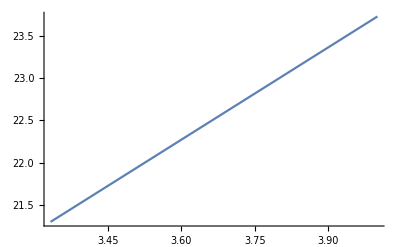

```mathematica
escapeTimesMark = {Log[Mean[EscTime]],Log[Mean[EscTime1]],Log[Mean[EscTime2]],Log[Mean[EscTime3]],Log[Mean[EscTime4]],Log[Mean[EscTime5]] };
ListLinePlot[Transpose[{1/temperatures,escapeTimesMark}]]
```

```mathematica
{Log[Mean[EscTime]], Log[Mean[EscTime5]]}
```

{23.727692392657355454331817013878368258966900970055,Log[Mean[EscTime5]]}

```mathematica
arrhenius[func_, temp_]:=Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,SetPrecision[TransMatrixFlint[temp,1,func,p],80]],7]]
```

```mathematica
arrhenius[f, temperatures[[1]]]
```

2.0174643744016221750953541497398127177859613360629×10^10

```mathematica
Table[arrhenius[f, i],temperatures]
```

Table::nliter: Non-list iterator temperatures at position 2 does not evaluate to a real numeric value.

Table[arrhenius[f,i],temperatures]

```mathematica
arrhenius[f,#]&/@temperatures
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

{Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{{0.9997765506744601864646053807723278072329965187139524136456363657352108613312072,0.0002234493255398135353946192276721927670034812860475863543636342647891386687928474,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},59,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,32,0,0,0,0,0,0,0,0,0,0,0,0,0.0003194501778056021325550628875410179263947781961123631731919840437684934717453698,0.9996805498221943978674449371124589820736052218038876368268080159562315065282546}}],70]],4,Mean[1]}
 |  |  |  |

```mathematica
Table[arrhenius[f,x],{x,temperatures}]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

{Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{{0.9997765506744601864646053807723278072329965187139524136456363657352108613312072,0.0002234493255398135353946192276721927670034812860475863543636342647891386687928474,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},59,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,32,0,0,0,0,0,0,0,0,0,0,0,0,0.0003194501778056021325550628875410179263947781961123631731919840437684934717453698,0.9996805498221943978674449371124589820736052218038876368268080159562315065282546}}],70]],4,Mean[1]}
 |  |  |  |

```mathematica
functions={f,f1}
```

{f,f1}

```mathematica
res = Table[arrhenius[f,x], {f, functions},{x,temperatures}]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

{{Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{{0.9997765506744601864802848820143917748280625671751346541514926721542448278302461,0.0002234493255398135197151179856082251719374328248653458485073278457551721697538951,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},59,{0,0,0,0,0,0,0,0,0,0,0,0,37,0,0,0,0,0,0,0,0,0,0,0.00031945017780560276162297207097297275401817301311002525806292555310463545143299,0.999680549822194397238377027929027027245981826986889974741937074446895364548567}}],70]],4,Mean[1]},1}
 |  |  |  |

```mathematica
ListLinePlot[{Transpose[{1/temperatures,Log[res[[1]]]}], Transpose[{1/temperatures,Log[res[[2]]]}]},PlotLegends->{"Griffith","Ising"}, Filling->Axis]
```

-Graphics-

{{-0.995044,-1.7118,-0.765699,-1.75935,-2.715,-2.43661,-2.21562,-2.22659,-1.52279,-1.98031},{0.874652,1.63794,1.62778,1.88388,1.95874,2.28849,2.59215,2.54902,2.24517,2.69173},{-0.827444,-0.908133,0.030197,-0.728449,-0.554139,-0.754944,-1.28404,-1.79375,-1.35355,-1.49486}}

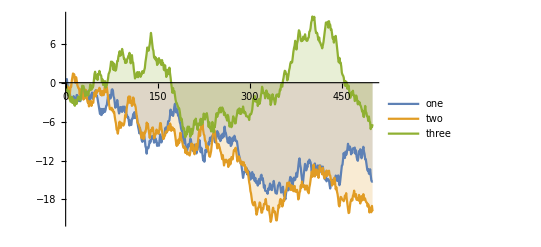

```mathematica
Table[Accumulate[RandomReal[{-1,1},10]],{3}]
ListLinePlot[Table[Accumulate[RandomReal[{-1,1},500]],{3}],Filling->Axis,PlotLegends->{"one","two","three"}]
```

```mathematica
ListLinePlot[Transpose[{1/temperatures,Log[res[[1]]]}],PlotLegends->{"Griffith","Ising"}]

Transpose[{1/temperatures,Log[res[[1]]]}]




func[f_,x_]:=f[x]
```

-Graphics-

{{4,Log[Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{{0.9997765506744601864802848820143917748280625671751346541514926721542448278302461,0.0002234493255398135197151179856082251719374328248653458485073278457551721697538951,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},60}],70]]]},{10/3,Log[Mean[1]]},{20/7,Log[1]},{1},{2,Log[Mean[1]]},{5/3,Log[Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{{0.9997178345263728458623222747679406046229538255507567695031693988164260847780068,59,0},60}],70]]]}}
 |  |  |  |

```mathematica
functest[x_]:=x^2
```

```mathematica
func [fava,2]
```

fava[2]

```mathematica
listval = {1,2,3}
```

{1,2,3}

```mathematica
ClearAll
```

ClearAll

```mathematica
listfuncobs={ #&, #^2&}
```

{#1&,#1^2&}

```mathematica
listfunc={SetDelayed[x[x],x^2[x]]}
```

{Null}

```mathematica
listfunc="g"<>ToString[#]&/@{1,2,3}//ToExpression;
```

```mathematica
Table[func[functest,x],{x,listval}]
```

{1,4,9}

```mathematica
Table[func[f[x],x], {f, listfunc},{x,listval}]
```

{{2[1],5[2],10[3]},{0[1],Log[2][2],Log[3][3]},{(2 Cos[1])[1],(2 Cos[2])[2],(2 Cos[3])[3]}}

```mathematica
listfunc1 = #[x]&/@listfunc


Table[func[f[x],x], {{f, listfunc1},{x,listval}}]
```

{1+x^2,Log[x],2 Cos[x]}

Table::write: Tag List in {f,listfunc1} is Protected.

Table[func[f[x],x],{{f,listfunc1},{x,{1,2,3}}}]

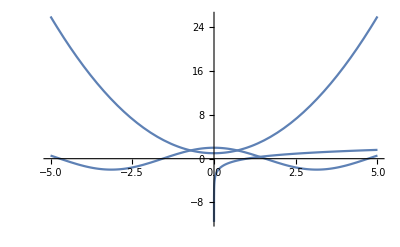

```mathematica
g1[x_]=x*x+1;
g2[x_]=Log[x];
g3[x_]=2 Cos[x];
funclist="g"<>ToString[#]&/@{1,2,3}//ToExpression;
Plot[#[x]&/@funclist,{x,-5,5}]
```

```mathematica
tem=Developer`ToPackedArray[{0.05,0.06,0.2,0.35,0.5}];
```

```mathematica
resDoubleWell=Table[arrhenius[doublewell,x],{x,tem}]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

{Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{{0.999666666666666666690031223483729286362042349166956929298613524001045530867015,0.0003333333333333333099687765162707136379576508330430707013864759989544691329849942,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},60}],70]],3,Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{{0.999666666666666666690031223483729286362042349166956929298613524001045530867015,59,0},59,{0,0,0,0,0,0,0,0,0,0,0,0,0,35,0,0,0,0,0,0,0,0,0,0,0,116,116}}],70]]}
 |  |  |  |

```mathematica
ListLinePlot[Transpose[{1/temperatures,Log[resDoubleWell]}],PlotLegends->{"Double Well"}]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{{4.,3.33333,2.85714,2.5,2.,1.66667},{Log[Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{«61»}],70]]],Log[Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{«61»}],70]]],Log[Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{«61»}],70]]],Log[Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{«61»}],70]]],Log[Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{«61»}],70]]]}}] is not a list of numbers or pairs of numbers.

ListLinePlot[Transpose[{{4,10/3,20/7,5/2,2,5/3},{Log[Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{{0.999666666666666666690031223483729286362042349166956929298613524001045530867015,0.0003333333333333333099687765162707136379576508330430707013864759989544691329849942,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},59,{0,0,58,0.999666666666666666690031223483729286362042349166956929298613524001045530867015}}],70]]],3,Log[Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,{1}],70]]]}}],PlotLegends→{Double Well}]
 |  |  |  |

```mathematica
points=Range[0,6,1]
```

{0,1,2,3,4,5,6}